```mathematica
(* These lines sets up Albedo as a function of time *)
Clear[f,g,h];
ice=0.55;
water =0.3;
meltpoint=273.15;
variance = 10;
f[t_]:=If[t≤0,0,E^(-1/t)];
g[t_]:=f[t]/(f[t]+f[1-t]);
h[t_]:=(water-ice)*g[(t-(meltpoint-variance))/(2*variance)]+ice
```

```mathematica
(* Constants and functios for the model *)
S=1367;
α=0.55;
σ=5.670374419*10^(-8);
ϵ=0.612;
Clear[t,a,b,x];
d1[t_,a_,b_] := a*t+b;
d2[t_]:=5*Log[t+1];
```

```mathematica
(* ONLY RUN THIS MODEL FOR THE BIFURCATION DIAGRAM, IT TAKES A VERY LONG TIME TO EXECUTE *)
funk[x_,y_]:={x,y};
roots=Table[{delta,T/.NSolve[S/4(1-h[T])-ϵ*σ*T^4+delta==0&&T≥ 0,T]},{delta,-30,30,0.1}]
roots2 = roots/.{x_,{y1_,y2_,y3_}}->{{x,y1},{x,y2},{x,y3}};
roots3 = Flatten[roots2,∞];
roots4 = ArrayReshape[roots3,{Length[roots3]/2,2}];
```

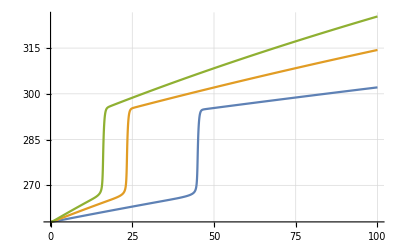

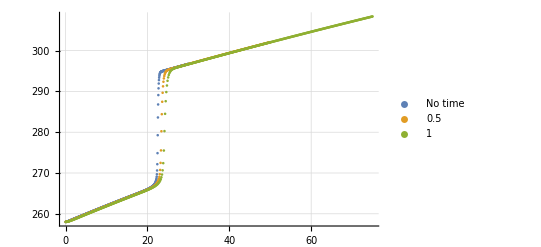

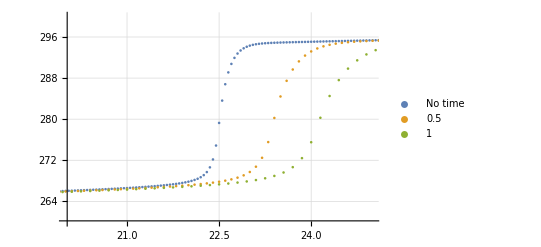

```mathematica
(* This part does not take long to execute *)
(* Uncomment next line to view the ΔT as a function of T *)
(* Plot[S/4(1-h[T])-ϵ*σ*T^4,{T,200,370},GridLines->Automatic] *)

(* The next lines computes the lower equilibrium if we want to compare with fixed bifurcation parameter*)
ass=NDSolve[{T'[t]==S/4(1-h[T[t]])-ϵ*σ*T[t]^4 ,T[0]==258},T,{t,0,100}];
eq = Evaluate[T[100]/.ass][[1]];

(* The next few lines are the solution to the differential model as a function of time. *)(* The first three are growing df at different speeds, the fourth starts at an offset df, the fifth one is logarithmic growth of df.*)
Clear[T,t,s,u,v,w,x]
s=NDSolve[{T'[t]==S/4(1-h[T[t]])-ϵ*σ*T[t]^4 +d1[t,0.5,0],T[0]==eq},T,{t,0,100}];
u=NDSolve[{T'[t]==S/4(1-h[T[t]])-ϵ*σ*T[t]^4 +d1[t,1,0],T[0]==eq},T,{t,0,100}];
v=NDSolve[{T'[t]==S/4(1-h[T[t]])-ϵ*σ*T[t]^4 +d1[t,1.5,0],T[0]==eq},T,{t,0,100}];
w=NDSolve[{T'[t]==S/4(1-h[T[t]])-ϵ*σ*T[t]^4 +d1[t,1,15],T[0]==eq},T,{t,0,100}];
x=NDSolve[{T'[t]==S/4(1-h[T[t]])-ϵ*σ*T[t]^4 +d2[t],T[0]==eq},T,{t,0,500}];

(* These lines plot T for growing df *)
ls11 = Table[{d1[t,0.5,0],T[t]/.s},{t,0,60,0.1}];
ls12 = Flatten /@ ls11;
ls21 = Table[{d1[t,1,0],T[t]/.u},{t,0,50,0.1}];
ls22 = Flatten /@ ls21;
ls31 = Table[{d1[t,1.5,0],T[t]/.v},{t,0,50,0.1}];
ls32 = Flatten /@ ls31;

(* These lines export the temperature growth as df grows *)
(* The final lines plot the tables above *)
SetDirectory[NotebookDirectory[]];
Export["05.csv",ls12];
Export["10.csv",ls22];
Export["15.csv",ls32];
Plot[{Evaluate[T[t]/.s],Evaluate[T[t]/.u],Evaluate[T[t]/.v]},{t,0,100},PlotRange->All,GridLines->Automatic]
ListPlot[{ls12,ls22,ls32},PlotRange->All,PlotLegends->{"No time",0.5,1,1.5},GridLines->Automatic]
ListPlot[{ls12,ls22,ls32},PlotRange->{{20,25},{260,300}},PlotLegends->{"No time",0.5,1,1.5},GridLines->Automatic]
```